# CanonicalPairPlane

## Canonical representatives and coordinates for nondegenerate first-harmonic data

## Purpose

This notebook supports the canonical pair-plane constructions in Chapter 3. It extracts the first-harmonic component of a polygon, assigns canonical coordinates to its nondegenerate pair-plane ellipse, constructs a canonical representative, and verifies invariance under translation, rotation, and nonzero scaling.

All executable cells are ordinary Wolfram Language Input cells. Typeset box expressions appear only in explanatory cells.

## 1. Fourier and pair-plane definitions

```mathematica
ClearAll["Global`*"];

omega[n_Integer?Positive] := Exp[2 Pi I/n];

fourierVector[n_Integer?Positive, k_Integer] :=
  Table[omega[n]^(j k), {j, 0, n - 1}]/Sqrt[n];

fourierMatrix[n_Integer?Positive] :=
  Transpose@Table[fourierVector[n, k], {k, 0, n - 1}];

fourierCoefficients[p_List] := Module[{F},
  F = fourierMatrix[Length[p]];
  ConjugateTranspose[F] . N[p]
];

fourierSynthesis[c_List] :=
  fourierMatrix[Length[c]] . c;

centerPolygon[p_List] :=
  N[p] - Mean[N[p]];

firstHarmonicData[p_List] := Module[{n, c},
  n = Length[p];
  c = fourierCoefficients[p];
  <|
    "c1" -> c[[2]],
    "cNMinus1" -> c[[n]]
  |>
];

pairPlaneProjection[p_List] := Module[{n, c, result},
  n = Length[p];
  c = fourierCoefficients[p];
  result = ConstantArray[0, n];
  result[[2]] = c[[2]];
  result[[n]] = c[[n]];
  fourierSynthesis[result]
];
```

```mathematica
nExample = 12;
SeedRandom[5151];
pExample = RandomReal[{-1, 1}, nExample] + I RandomReal[{-1, 1}, nExample];
pExample = centerPolygon[pExample];
pPair = pairPlaneProjection[pExample];
```

## 2. Nondegenerate pair-plane data

For

p_(±1)=c_1 φ_1+c_(n-1)φ_(n-1)

nondegeneracy means

|c_1|≠|c_(n-1)|

```mathematica
nondegeneratePairPlaneQ[p_List, tol_: 10^-10] := Module[{data},
  data = firstHarmonicData[p];
  TrueQ[Abs[Abs[data["c1"]] - Abs[data["cNMinus1"]]] > tol]
];
```

```mathematica
nondegeneratePairPlaneQ[pExample]
```

True

## 3. Canonical pair-plane coordinates

The canonical data are the ordered semi-axis lengths, the orientation angle, and the phase angle.

```mathematica
canonicalPairCoordinates[p_List] := Module[
  {data, c1, cN, r1, rN, theta1, thetaN, major, minor, orientation, phase},
  data = firstHarmonicData[p];
  c1 = data["c1"];
  cN = data["cNMinus1"];
  r1 = Abs[c1];
  rN = Abs[cN];
  theta1 = Arg[c1];
  thetaN = Arg[cN];
  major = r1 + rN;
  minor = Abs[r1 - rN];
  orientation = Mod[(theta1 + thetaN)/2, Pi];
  phase = Mod[(theta1 - thetaN)/2, 2 Pi];
  <|
    "c1" -> c1,
    "cNMinus1" -> cN,
    "MajorAxis" -> major,
    "MinorAxis" -> minor,
    "AxisRatio" -> If[minor == 0, Infinity, major/minor],
    "Orientation" -> orientation,
    "Phase" -> phase,
    "OrientationSign" -> Sign[r1 - rN]
  |>
];
```

```mathematica
coordsExample = canonicalPairCoordinates[pExample];
coordsExample
```

<|c1→-0.336745+1.1495 ⅈ,cNMinus1→0.235734-0.396875 ⅈ,MajorAxis→1.65942,MinorAxis→0.736205,AxisRatio→2.25402,Orientation→0.410476,Phase→1.44529,OrientationSign→1|>

## 4. Canonical coefficient representative

After removing overall orientation and phase, a nondegenerate pair-plane element may be represented by real coefficients whose sum and difference are the semi-axis lengths.

```mathematica
canonicalCoefficients[p_List] := Module[{coords, a, b, s},
  coords = canonicalPairCoordinates[p];
  a = coords["MajorAxis"];
  b = coords["MinorAxis"];
  s = coords["OrientationSign"];
  <|
    "c1Canonical" -> (a + s b)/2,
    "cNMinus1Canonical" -> (a - s b)/2
  |>
];
```

```mathematica
canonicalCoefficients[pExample]
```

<|c1Canonical→1.19781,cNMinus1Canonical→0.461607|>

## 5. Canonical pair-plane representative

```mathematica
canonicalPairRepresentative[p_List] := Module[{n, coeffs, c},
  n = Length[p];
  coeffs = canonicalCoefficients[p];
  c = ConstantArray[0, n];
  c[[2]] = coeffs["c1Canonical"];
  c[[n]] = coeffs["cNMinus1Canonical"];
  fourierSynthesis[c]
];
```

```mathematica
canonicalExample = canonicalPairRepresentative[pExample];
```

## 6. Reconstruction map

The original first harmonic is recovered from the canonical representative by reintroducing orientation and phase.

```mathematica
reconstructPairFromCanonical[canonical_List, coords_Association] := Module[
  {n, c, c1Canonical, cNCanonical, psi, delta, result},
  n = Length[canonical];
  c = fourierCoefficients[canonical];
  c1Canonical = c[[2]];
  cNCanonical = c[[n]];
  psi = coords["Orientation"];
  delta = coords["Phase"];
  result = ConstantArray[0, n];
  result[[2]] = c1Canonical Exp[I (psi + delta)];
  result[[n]] = cNCanonical Exp[I (psi - delta)];
  fourierSynthesis[result]
];
```

```mathematica
reconstructedPair = reconstructPairFromCanonical[canonicalExample, coordsExample];
reconstructionError = Norm[N[reconstructedPair - pPair]];
reconstructionQ = reconstructionError < 10^-10;
```

```mathematica
reconstructionError
```

4.26615×10^-16

```mathematica
reconstructionQ
```

True

## 7. Scale-free canonical representative

Dividing by the major semi-axis removes overall size. The resulting representative is determined by the minor-to-major axis ratio.

```mathematica
scaleFreeCanonicalRepresentative[p_List] := Module[{canonical, major},
  canonical = canonicalPairRepresentative[p];
  major = canonicalPairCoordinates[p]["MajorAxis"];
  canonical/major
];

shapeParameter[p_List] := Module[{coords},
  coords = canonicalPairCoordinates[p];
  coords["MinorAxis"]/coords["MajorAxis"]
];
```

```mathematica
{
  shapeParameter[pExample],
  Norm[scaleFreeCanonicalRepresentative[pExample]]
}
```

{0.443652,0.773572}

## 8. Similarity invariance

Translation, nonzero complex scaling, and rotation do not change the scale-free canonical shape.

```mathematica
similarityTransform[p_List, eta_, z0_] :=
  eta N[p] + z0;

etaExample = 2.4 Exp[0.73 I];
z0Example = -1.1 + 0.8 I;
pTransformed = similarityTransform[pExample, etaExample, z0Example];
```

```mathematica
shapeInvariantError = Norm[N[
  scaleFreeCanonicalRepresentative[pExample] -
  scaleFreeCanonicalRepresentative[pTransformed]
]];
shapeInvariantQ = shapeInvariantError < 10^-10;
```

```mathematica
shapeInvariantError
```

1.78803×10^-16

```mathematica
shapeInvariantQ
```

True

## 9. Coordinate transformation under similarity

```mathematica
coordsTransformed = canonicalPairCoordinates[pTransformed];
coordinateComparison = <|
  "AxisRatioOriginal" -> coordsExample["AxisRatio"],
  "AxisRatioTransformed" -> coordsTransformed["AxisRatio"],
  "OrientationShift" -> Mod[
    coordsTransformed["Orientation"] - coordsExample["Orientation"],
    Pi
  ],
  "ExpectedOrientationShift" -> Mod[Arg[etaExample], Pi],
  "ScaleFactor" -> coordsTransformed["MajorAxis"]/coordsExample["MajorAxis"],
  "ExpectedScaleFactor" -> Abs[etaExample]
|>;
coordinateComparison
```

<|AxisRatioOriginal→2.25402,AxisRatioTransformed→2.25402,OrientationShift→0.73,ExpectedOrientationShift→0.73,ScaleFactor→2.4,ExpectedScaleFactor→2.4|>

```mathematica
orientationShiftError = Abs[N[
  Sin[
    coordinateComparison["OrientationShift"] -
    coordinateComparison["ExpectedOrientationShift"]
  ]
]];
scaleFactorError = Abs[N[
  coordinateComparison["ScaleFactor"] -
  coordinateComparison["ExpectedScaleFactor"]
]];
```

```mathematica
{orientationShiftError, scaleFactorError}
```

{1.11022×10^-16,0.}

## 10. Canonical uniqueness test

Two nondegenerate first-harmonic polygons have the same scale-free canonical representative exactly when their pair-plane ellipses differ only by translation and nonzero complex scaling.

```mathematica
sameCanonicalShapeQ[p_List, q_List, tol_: 10^-10] :=
  TrueQ[
    Norm[N[
      scaleFreeCanonicalRepresentative[p] -
      scaleFreeCanonicalRepresentative[q]
    ]] < tol
  ];
```

```mathematica
{
  sameCanonicalShapeQ[pExample, pTransformed],
  sameCanonicalShapeQ[pExample, pExample + 0.2 fourierVector[nExample, 2]]
}
```

{True,True}

## 11. Canonical pair-plane basis coordinates

```mathematica
canonicalBasisCoordinates[p_List] := Module[{canonical, c, n},
  canonical = canonicalPairRepresentative[p];
  n = Length[p];
  c = fourierCoefficients[canonical];
  {c[[2]], c[[n]]}
];
```

```mathematica
canonicalBasisCoordinates[pExample]
```

{1.19781+0. ⅈ,0.461607-1.38778×10^-17 ⅈ}

## 12. Axis-ratio and eccentricity invariants

```mathematica
canonicalEccentricity[p_List] := Module[{q},
  q = shapeParameter[p];
  Sqrt[Max[0, 1 - q^2]]
];

{
  shapeParameter[pExample],
  canonicalEccentricity[pExample],
  canonicalEccentricity[pTransformed]
}
```

{0.443652,0.896199,0.896199}

## 13. Visualization

```mathematica
complexPoints[p_List] :=
  N@Transpose[{Re[N[p]], Im[N[p]]}];

polygonGraphic[p_List, title_] := Module[{pts},
  pts = complexPoints[p];
  Graphics[
    {
      Thick,
      Line[Append[pts, First[pts]]],
      PointSize[0.018],
      Point[pts]
    },
    Axes -> True,
    AspectRatio -> 1,
    PlotRange -> All,
    PlotLabel -> title,
    ImageSize -> Large
  ]
];
```

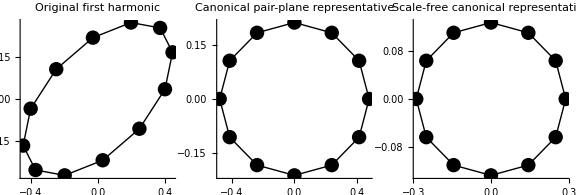

```mathematica
GraphicsRow[
  {
    polygonGraphic[pPair, "Original first harmonic"],
    polygonGraphic[canonicalExample, "Canonical pair-plane representative"],
    polygonGraphic[
      scaleFreeCanonicalRepresentative[pExample],
      "Scale-free canonical representative"
    ]
  },
  ImageSize -> Large
]
```

## 14. Representative family

```mathematica
shapeParameters = {0.1, 0.3, 0.5, 0.7, 0.9};
representativeFamily = Table[
  Module[{c},
    c = ConstantArray[0, nExample];
    c[[2]] = (1 + q)/2;
    c[[nExample]] = (1 - q)/2;
    fourierSynthesis[c]
  ],
  {q, shapeParameters}
];
```

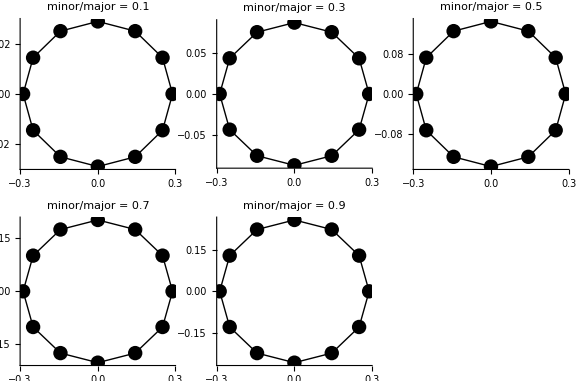

```mathematica
GraphicsGrid[
  Partition[
    MapThread[
      polygonGraphic[#1, Row[{"minor/major = ", #2}]] &,
      {representativeFamily, shapeParameters}
    ],
    3,
    3,
    {1, 1},
    Nothing
  ],
  ImageSize -> Large
]
```

## 15. Automated verification report

```mathematica
Clear[verificationReport];

verificationReport[] := verificationReport[20];

verificationReport[maxN_Integer?Positive] := Module[{rows},
  rows = Table[
    Module[
      {p, pair, coords, canonical, reconstructed, eta, z0, transformed, reconstructionError, invariantError, scaleError},
      SeedRandom[8000 + n];
      p = RandomReal[{-1, 1}, n] + I RandomReal[{-1, 1}, n];
      p = centerPolygon[p];
      If[!nondegeneratePairPlaneQ[p, 10^-6],
        p = p + 0.2 fourierVector[n, 1]
      ];
      pair = pairPlaneProjection[p];
      coords = canonicalPairCoordinates[p];
      canonical = canonicalPairRepresentative[p];
      reconstructed = reconstructPairFromCanonical[canonical, coords];
      eta = 1.8 Exp[0.4 I];
      z0 = 0.7 - 0.3 I;
      transformed = similarityTransform[p, eta, z0];
      reconstructionError = Norm[N[reconstructed - pair]];
      invariantError = Norm[N[
        scaleFreeCanonicalRepresentative[p] -
        scaleFreeCanonicalRepresentative[transformed]
      ]];
      scaleError = Abs[N[
        canonicalPairCoordinates[transformed]["MajorAxis"]/
        canonicalPairCoordinates[p]["MajorAxis"] - Abs[eta]
      ]];
      <|
        "n" -> n,
        "Nondegenerate pair-plane" -> TrueQ[nondegeneratePairPlaneQ[p]],
        "Canonical reconstruction" -> TrueQ[reconstructionError < 10^-9],
        "Similarity invariance" -> TrueQ[invariantError < 10^-9],
        "Scale covariance" -> TrueQ[scaleError < 10^-9]
      |>
    ],
    {n, 5, maxN}
  ];
  Dataset[rows]
];
```

```mathematica
verificationReport[]
```

## Conclusion

The canonical pair-plane construction separates intrinsic shape from translation, rotation, and scale. A nondegenerate first harmonic is represented canonically by its ordered semi-axis data, or equivalently by a scale-free minor-to-major ratio together with a fixed real Fourier coefficient pair. Reconstruction restores orientation, phase, and size.